## Population Dynamics under Indirect Reciprocity

## Variables

```mathematica
socialnorm= {1,0,0,0};  (*Social norm is defined as d = (d_gc, d_gd, d_bc, d_bd), where d_rs is the chance of assigning G to an indiv who did S agaisnt a R*)
simplexFileName = "SH_AA4_";
(*Image-Score (IS)[1,0,1,0];
Simple-Standing (SS)[1,0,1,1];
Shunning (SH)[1,0,0,0];
Stern-Judging (SJ)[1,0,0,1]*)

popsize= 100;  (* Size of the population *)
sampleSize = 25;
fractionOfAAs =  N[1/25](*0.0*);
AAsPop = "Disc";

fixedAAstrategy= True; (*If true, AAs have fixed reputations*)
fixedAAreputations = False; (*If true, AAs have fixed reputations*)
fixedAARep = "G";                     (*The fixed reputations the AAs have*)

nAAs = Round[popsize*fractionOfAAs]; (*Real number of AAs in the population. To control the strategy see section on TplusStrat and Strategy Transition Matrix*)
indexOfAA=Which[AAsPop=="AllC",0,AAsPop=="AllD",1,True,2];(* Used to index states using just the AA type*)

errorAssign= 0.01;    (* Prob. of assigning the wrong reputation after an observation *)
errorExecut= 0.01;    (* Prob. of executing the wrong action *)
errorAssess= 0.01;    (* Prob. of incorrectly acessing the other's reputation before chosing an action *)

strengthOfSelection = 1; 
mutationChance = N[1/popsize];

(* Donation game parameters *)
b = 2;  (* benefit *)
c = 1;  (* cost of cooperation *)

(* Strategies, where p(G,B) = (prob of cooperating against Good, " against Bad) *)
allC= {1,1};
allD= {0,0};
disc= {1,0};

(* Add execution error to strategies *) 
addExecError[strat_] := (1-2*errorExecut)*strat+errorExecut;
allC = {addExecError[allC[[1]]],addExecError[allC[[2]]]};
allD = {addExecError[allD[[1]]],addExecError[allD[[2]]]};
disc = {addExecError[disc[[1]]],addExecError[disc[[2]]]};

(* Add assignment error to social norm *)
addError[socialn_] := (1-2*errorAssign)*socialn+errorAssign;
socialnorm = {addError[socialnorm[[1]]],addError[socialnorm[[2]]],addError[socialnorm[[3]]],addError[socialnorm[[4]]]};
```

## Calculate Reputation Dynamics

```mathematica
(* Chances of cooperation when user of strat S sees a G, considering errors *) 
coopSG[strategy_] := coopSG[strategy] =(1-errorAssess) * strategy[[1]] + errorAssess * strategy[[2]]
coopSB[strategy_] := coopSB[strategy] =errorAssess * strategy[[1]] +(1- errorAssess) * strategy[[2]]

(* Reputation update prob, the probability that one observer assigns a good reputation to an individual using strategy s and interacting with a good/bad opponent is given by*)
assignGG[strategy_] := assignGG[strategy] = (1-errorAssess)*(coopSG[strategy]*socialnorm[[1]]+(1-coopSG[strategy])*socialnorm[[2]])+errorAssess*(coopSG[strategy]*socialnorm[[3]]+(1-coopSG[strategy])*socialnorm[[4]])
assignGB[strategy_] := assignGB[strategy] = errorAssess*(coopSB[strategy]*socialnorm[[1]]+(1-coopSB[strategy])*socialnorm[[2]])+(1-errorAssess)*(coopSB[strategy]*socialnorm[[3]]+(1-coopSB[strategy])*socialnorm[[4]])


(* Birth death probabilities given gAllC good AllCs (out of nAllC), and so on*)
commonFactorTPlus[strat_,nAllC_, gAllC_,nAllD_, gAllD_,gDisc_,popsample_]:= commonFactorTPlus[strat,nAllC, gAllC,nAllD, gAllD,gDisc,popsample]=
(gAllC+gAllD+gDisc)/(popsample-1)*assignGG[strat]+(popsample-gAllC-gAllD-gDisc-1)/(popsample-1)*assignGB[strat]

commonFactorTMinus[strat_,nAllC_, gAllC_,nAllD_, gAllD_,gDisc_,popsample_]:= commonFactorTMinus[strat,nAllC, gAllC,nAllD, gAllD,gDisc,popsample] =(gAllC+gAllD+gDisc-1)/(popsample-1)*(1-assignGG[strat])+(popsample-gAllC-gAllD-gDisc)/(popsample-1)*(1-assignGB[strat])

dampFactorPlus[pop_,AAs_]:=If[fixedAAreputations && indexOfAA == pop,If[fixedAARep == "G",0,AAs],0];
dampFactorMinus[pop_,AAs_]:=If[fixedAAreputations && indexOfAA == pop,If[fixedAARep == "B",0,AAs],0];


TplusRepAllC[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_,popsample_,AAs_] := ((nAllC-gAllC-dampFactorPlus[0,AAs])/popsample)*commonFactorTPlus[allC,nAllC, gAllC,nAllD, gAllD,gDisc,popsample]
TminusRepAllC[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_,popsample_,AAs_] := ((gAllC-dampFactorMinus[0,AAs])/popsample)*commonFactorTMinus[allC,nAllC, gAllC,nAllD, gAllD,gDisc,popsample]

TplusRepAllD[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_,popsample_,AAs_] := ((nAllD-gAllD-dampFactorPlus[1,AAs])/popsample)*commonFactorTPlus[allD,nAllC, gAllC,nAllD, gAllD,gDisc,popsample]
TminusRepAllD[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_,popsample_,AAs_] := ((gAllD-dampFactorMinus[1,AAs])/popsample)*commonFactorTMinus[allD,nAllC, gAllC,nAllD, gAllD,gDisc,popsample]

TplusRepDisc[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_,popsample_,AAs_] := ((popsample-nAllC-nAllD-gDisc-dampFactorPlus[2,AAs])/popsample)*commonFactorTPlus[disc,nAllC, gAllC,nAllD, gAllD,gDisc,popsample]
TminusRepDisc[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_,popsample_,AAs_] := ((gDisc-dampFactorMinus[2,AAs])/popsample)*commonFactorTMinus[disc,nAllC, gAllC,nAllD, gAllD,gDisc,popsample]

TequalsRep[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_,popsample_,AAs_]  := 1 - TplusRepAllC[nAllC, gAllC,nAllD, gAllD,gDisc,popsample,AAs]- TminusRepAllC[nAllC, gAllC,nAllD, gAllD,gDisc,popsample,AAs]- TplusRepAllD[nAllC, gAllC,nAllD, gAllD,gDisc,popsample,AAs]- TminusRepAllD[nAllC, gAllC,nAllD, gAllD,gDisc,popsample,AAs]- TplusRepDisc[nAllC, gAllC,nAllD, gAllD,gDisc,popsample,AAs]- TminusRepDisc[nAllC, gAllC,nAllD, gAllD,gDisc,popsample,AAs]

(* Calculate transition matrix between all states of reputation distribution. Start with 0s and add all cases of states where gAllC -> gAllC+1 and etc.
Note: Since this depends on the number of AllCs, AllDs, and Disc, all this must be a function! We gotta calculate it for each step... *)

getPopNumber[nAllC_,nAllD_,popsample_]:=If[indexOfAA==0,nAllC,If[indexOfAA==1,nAllD,popsample-nAllC-nAllD]]; (*Given an indexOfAA, returns the respective number of the population*)

getStates[nAllC_,nAllD_,popsample_] := getStates[nAllC,nAllD,popsample] = Flatten[Table[{i,j,k},{i,0,nAllC},{j,0,nAllD},{k,0,popsample-nAllC-nAllD}],2];
getFilteredRepStates[nAllC_,nAllD_,popsample_,AAs_] := getFilteredRepStates[nAllC,nAllD,popsample,AAs] = If[fixedAAreputations,Select[getStates[nAllC,nAllD,popsample] ,Which[
fixedAARep == "G",#[[indexOfAA+1]]>=AAs,
fixedAARep == "B",getPopNumber[nAllC,nAllD,popsample]-#[[indexOfAA+1]]>=AAs,
True,False]&],getStates[nAllC,nAllD,popsample] ];

posOfState[states_,state_] := Position[states,state][[1,1]];

CalculateStationaryDistRep[nAllC_,nAllD_,popsample_,AAs_]:= CalculateStationaryDistRep[nAllC,nAllD,popsample,AAs] =Module[{states, transitionMatrix, largestVec, result, t1,t2,t3,t4,t5,t6},
states=getFilteredRepStates[nAllC,nAllD,popsample,AAs];(*Filter for states with AAs*)

transitionMatrix=SparseArray[{},{Length[states],Length[states]}];
(* Do each transition case*)
Do[
t1 = t2 = t3 = t4 = t5 = t6 = 0; (* Variables used to save computation time on Tequals*)
(*Dont calculate illegal fixed rep states*)
If[fixedAAreputations && Not[MemberQ[states,{i,j,k}]], Continue[]];

(*Add or remove AllC*)
If[i<nAllC && MemberQ[states,{i+1,j,k}],transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i+1,j,k}][[1,1]]]]= t1= TplusRepAllC[nAllC,i,nAllD,j,k,popsample,AAs]];
If[i>0 && MemberQ[states,{i-1,j,k}],transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i-1,j,k}][[1,1]]]]= t2= TminusRepAllC[nAllC,i,nAllD,j,k,popsample,AAs]];

(*Add or remove AllD*)
If[j<nAllD && MemberQ[states,{i,j+1,k}],transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i,j+1,k}][[1,1]]]]=t3=TplusRepAllD[nAllC,i,nAllD,j,k,popsample,AAs]];
If[j>0 && MemberQ[states,{i,j-1,k}],transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i,j-1,k}][[1,1]]]]=t4=TminusRepAllD[nAllC,i,nAllD,j,k,popsample,AAs]];

(*Add or remove Disc*)
If[k<popsample-nAllC-nAllD && MemberQ[states,{i,j,k+1}],transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i,j,k+1}][[1,1]]]]=t5=TplusRepDisc[nAllC,i,nAllD,j,k,popsample,AAs]];
If[k>0 && MemberQ[states,{i,j,k-1}],transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i,j,k-1}][[1,1]]]]=t6=TminusRepDisc[nAllC,i,nAllD,j,k,popsample,AAs]];

(*Stay in the same state*)
(*transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i,j,k}][[1,1]]]]=TequalsRep[nAllC,i,nAllD,j,k];*)
transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i,j,k}][[1,1]]]]= 1-t1-t2-t3-t4-t5-t6; (*To combat edge cases, it is better to make tEqual always based on the used values for the other transitions.*)

(*Everything else: if it starts at 0, everything is already fine *)
,{i,0,nAllC},{j,0,nAllD},{k,0,popsample-nAllC-nAllD}];

(* Calculate stationary distribution of good and bad in each strategy. Assumes we start with everyone G, but it shouldn't matter since its an ergodic chain *)
largestVec:=Eigenvectors[Transpose[transitionMatrix],1,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]];
result := Abs[largestVec]/Total[Abs[largestVec]];

result
];

AverageRepStateScaled[nAllC_,nAllD_,popsample_,AAs_] :=AverageRepStateScaled[nAllC,nAllD,popsample]  = Module[{states,statDist, pos, result},
states=getFilteredRepStates[nAllC,nAllD,sampleSize,AAs];
statDist = CalculateStationaryDistRep[nAllC,nAllD,sampleSize,AAs];
result={0.0,0.0,0.0};
result = Total[statDist #]&/@Transpose[states];
result
]
AverageRepState[nAllC_,nAllD_] := Module[{populationRatio,newNAAs,newNAllC,newNAllD,result},
populationRatio=N[sampleSize/popsize];
newNAAs=Round[nAAs*populationRatio];
newNAllC=Round[nAllC*populationRatio];
newNAllD=Round[nAllD*populationRatio];
If[sampleSize-newNAllC-newNAllD<0,If[newNAllC>newNAllD,newNAllC-=1,newNAllD-=1]];

allCRatio=If[nAllC == 0, 1, newNAllC/nAllC];
allDRatio=If[nAllD == 0 , 1, newNAllD/nAllD];
discRatio=If[popsize-nAllC-nAllD == 0, 1, (sampleSize-newNAllC-newNAllD)/(popsize-nAllC-nAllD) ];

result=AverageRepStateScaled[newNAllC,newNAllD,sampleSize,newNAAs];
result/={allCRatio,allDRatio,discRatio};
result=result/. Indeterminate->0;

Return[result];
]
```

## Calculate Strategy Dynamics

```mathematica
(* Change of strat p receiving donation: Prob = chance of being good and the opponent cooperates with good + chance of being bad and player cooperates with bads *)
AllCReceives[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_]:= AllCReceives[nAllC, gAllC,nAllD, gAllD,gDisc]= (gAllC/nAllC)*(
((nAllC-1)/(popsize-1))*coopSG[allC]+(nAllD/(popsize-1))*coopSG[allD]+((popsize-nAllC-nAllD)/(popsize-1))*coopSG[disc])+
((nAllC-gAllC)/nAllC)*(
((nAllC-1)/(popsize-1))*coopSB[allC]+(nAllD/(popsize-1))*coopSB[allD]+((popsize-nAllC-nAllD)/(popsize-1))*coopSB[disc]);
AllDReceives[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_]:= AllDReceives[nAllC, gAllC,nAllD, gAllD,gDisc]= (gAllD/nAllD)*(
(nAllC/(popsize-1))*coopSG[allC]+((nAllD-1)/(popsize-1))*coopSG[allD]+((popsize-nAllC-nAllD)/(popsize-1))*coopSG[disc])+
((nAllD-gAllD)/nAllD)*(
(nAllC/(popsize-1))*coopSB[allC]+((nAllD-1)/(popsize-1))*coopSB[allD]+((popsize-nAllC-nAllD)/(popsize-1))*coopSB[disc]);
DiscReceives[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_]:= DiscReceives[nAllC, gAllC,nAllD, gAllD,gDisc]=(gDisc/(popsize-nAllC-nAllD))*(
(nAllC/(popsize-1))*coopSG[allC]+(nAllD/(popsize-1))*coopSG[allD]+((popsize-nAllC-nAllD-1)/(popsize-1))*coopSG[disc])+
((popsize-nAllC-nAllD-gDisc)/(popsize-nAllC-nAllD))*(
(nAllC/(popsize-1))*coopSB[allC]+(nAllD/(popsize-1))*coopSB[allD]+((popsize-nAllC-nAllD-1)/(popsize-1))*coopSB[disc]);

(* Change of strat p donates *)
AllCDonates[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_] := AllCDonates[nAllC, gAllC,nAllD, gAllD,gDisc] =If[nAllC==0,0, gAllC/nAllC*((gAllC+gAllD+gDisc-1)/(popsize-1)*coopSG[allC]+(popsize-gAllC-gAllD-gDisc)/(popsize-1)*coopSB[allC])+
(nAllC-gAllC)/nAllC*((gAllC+gAllD+gDisc)/(popsize-1)*coopSG[allC]+(popsize-gAllC-gAllD-gDisc-1)/(popsize-1)*coopSB[allC])];
AllDDonates[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_] :=AllDDonates[nAllC, gAllC,nAllD, gAllD,gDisc] =If[nAllD==0,0,  gAllD/nAllD*((gAllC+gAllD+gDisc-1)/(popsize-1)*coopSG[allD]+(popsize-gAllC-gAllD-gDisc)/(popsize-1)*coopSB[allD])+
(nAllD-gAllD)/nAllD*((gAllC+gAllD+gDisc)/(popsize-1)*coopSG[allD]+(popsize-gAllC-gAllD-gDisc-1)/(popsize-1)*coopSB[allD])];
DiscDonates[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_] :=DiscDonates[nAllC, gAllC,nAllD, gAllD,gDisc] =  If[popsize-nAllC-nAllD==0,0,gDisc/(popsize-nAllC-nAllD)*((gAllC+gAllD+gDisc-1)/(popsize-1)*coopSG[disc]+(popsize-gAllC-gAllD-gDisc)/(popsize-1)*coopSB[disc])+
(popsize-nAllC-nAllD-gDisc)/(popsize-nAllC-nAllD)*((gAllC+gAllD+gDisc)/(popsize-1)*coopSG[disc]+(popsize-gAllC-gAllD-gDisc-1)/(popsize-1)*coopSB[disc])];


(* Add to get fitness of each strat in each state (Strategies X Reps) *)
fitAllC[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_] := If [nAllC == 0,0, b*AllCReceives[nAllC, gAllC,nAllD, gAllD,gDisc]-c*AllCDonates[nAllC, gAllC,nAllD, gAllD,gDisc]];
fitAllD[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_] := If [nAllD == 0,0, b*AllDReceives[nAllC, gAllC,nAllD, gAllD,gDisc]-c*AllDDonates[nAllC, gAllC,nAllD, gAllD,gDisc]];
fitDisc[nAllC_, gAllC_,nAllD_, gAllD_,gDisc_] := If [popsize-nAllC-nAllD == 0,0, b*DiscReceives[nAllC, gAllC,nAllD, gAllD,gDisc]-c*DiscDonates[nAllC, gAllC,nAllD, gAllD,gDisc]];

(* Calculate the average fitness considering the stationary distribution of reputations in each state *)
(* Current problem: How to combine stationary dist with fitness?*)
avgFitnessAllC[nAllC_,nAllD_] := Module[{avgRep},
avgRep = AverageRepState[nAllC,nAllD];
fitAllC[nAllC,avgRep[[1]],nAllD,avgRep[[2]],avgRep[[3]]]
]
avgFitnessAllD[nAllC_,nAllD_] := Module[{avgRep},
avgRep = AverageRepState[nAllC,nAllD];
fitAllD[nAllC,avgRep[[1]],nAllD,avgRep[[2]],avgRep[[3]]]
]
avgFitnessDisc[nAllC_,nAllD_] := Module[{avgRep},
avgRep = AverageRepState[nAllC,nAllD];
fitDisc[nAllC,avgRep[[1]],nAllD,avgRep[[2]],avgRep[[3]]]
]

(* Imitation probability (Fermi prob.), agent with strat A imitating agent B*)
pImit[fA_,fB_] := Power[(1+Power[E, -strengthOfSelection*(fB-fA)]),-1];

(*Calculate damping factor considering the existance of nAAs. Factor only applies in transitions to and from the strategy where AAs apply*)
dampFactorAllC[nAllC_,nAllD_] := If[indexOfAA == 0 && fixedAAstrategy,If[nAllC<nAAs,0,If[nAllC == 0,1,(nAllC-nAAs)/nAllC]],1];
dampFactorAllD[nAllC_,nAllD_] := If[indexOfAA == 1&& fixedAAstrategy,If[nAllD<nAAs,0,If[nAllD == 0,1,(nAllD-nAAs)/nAllD]],1];
dampFactorDisc[nAllC_,nAllD_] := If[indexOfAA == 2&& fixedAAstrategy,If[popsize-nAllC-nAllD<nAAs,0,If[popsize-nAllC-nAllD == 0,1,(popsize-nAllC-nAllD-nAAs)/(popsize-nAllC-nAllD),0]],1];


(* Given average fitness, define chance of changing from strategy X to Y (either through imitation and mutation) *)
(* Transitions to AllC*)
TAllDAllC[nAllC_,nAllD_] := TAllDAllC[nAllC,nAllD]= dampFactorAllD[nAllC,nAllD] *((1-mutationChance)*nAllD/popsize*nAllC/(popsize-1)*pImit[avgFitnessAllD[nAllC,nAllD],avgFitnessAllC[nAllC,nAllD]]+mutationChance*nAllD/(2*popsize));
TDiscAllC[nAllC_,nAllD_] := TDiscAllC[nAllC,nAllD]=dampFactorDisc[nAllC,nAllD] * ((1-mutationChance)*(popsize-nAllD-nAllC)/popsize*nAllC/(popsize-1)*pImit[avgFitnessDisc[nAllC,nAllD],avgFitnessAllC[nAllC,nAllD]]+mutationChance*(popsize-nAllD-nAllC)/(2*popsize));
(* Transitions to AllD*)
TAllCAllD[nAllC_,nAllD_] := TAllCAllD[nAllC,nAllD]= dampFactorAllC[nAllC,nAllD]*((1-mutationChance)*nAllC/popsize*nAllD/(popsize-1)*pImit[avgFitnessAllC[nAllC,nAllD],avgFitnessAllD[nAllC,nAllD]]+mutationChance*nAllC/(2*popsize))
TDiscAllD[nAllC_,nAllD_] :=TDiscAllD[nAllC,nAllD]=  dampFactorDisc[nAllC,nAllD]*((1-mutationChance)*(popsize-nAllD-nAllC)/popsize*nAllD/(popsize-1)*pImit[avgFitnessDisc[nAllC,nAllD],avgFitnessAllD[nAllC,nAllD]]+mutationChance*(popsize-nAllD-nAllC)/(2*popsize));
(* Transitions to Disc*)
TAllCDisc[nAllC_,nAllD_] :=TAllCDisc[nAllC,nAllD]=dampFactorAllC[nAllC,nAllD]* ((1-mutationChance)*nAllC/popsize*(popsize-nAllD-nAllC)/(popsize-1)*pImit[avgFitnessAllC[nAllC,nAllD],avgFitnessDisc[nAllC,nAllD]]+mutationChance*nAllC/(2*popsize));
TAllDDisc[nAllC_,nAllD_] := TAllDDisc[nAllC,nAllD] =dampFactorAllD[nAllC,nAllD] *((1-mutationChance)*nAllD/popsize*(popsize-nAllD-nAllC)/(popsize-1)*pImit[avgFitnessAllD[nAllC,nAllD],avgFitnessDisc[nAllC,nAllD]]+mutationChance*nAllD/(2*popsize));

(* Chance of increasing the number of agents in a single strategy (basically, Chance of +1 AllC = Chance AllD->AllC + Chance Disc->AllC)*)
TplusStratAllC[nAllC_,nAllD_] := TAllDAllC[nAllC,nAllD] + TDiscAllC[nAllC,nAllD];
TminusStratAllC[nAllC_,nAllD_] := TAllCAllD[nAllC,nAllD] + TAllCDisc[nAllC,nAllD];

TplusStratAllD[nAllC_,nAllD_] := TAllCAllD[nAllC,nAllD] + TDiscAllD[nAllC,nAllD];
TminusStratAllD[nAllC_,nAllD_] := TAllDAllC[nAllC,nAllD] + TAllDDisc[nAllC,nAllD];

TplusStratDisc[nAllC_,nAllD_] := TAllDDisc[nAllC,nAllD] + TAllCDisc[nAllC,nAllD];
TminusStratDisc[nAllC_,nAllD_] := TDiscAllD[nAllC,nAllD] + TDiscAllC[nAllC,nAllD];

(* Calculate gradients for each state based on state transitions *)
SelectionGradient[nAllC_,nAllD_] := {TplusStratAllC[nAllC,nAllD]-TminusStratAllC[nAllC,nAllD],TplusStratAllD[nAllC,nAllD]-TminusStratAllD[nAllC,nAllD]};
SelectionGradient3D[nAllC_,nAllD_] := {TplusStratAllC[nAllC,nAllD]-TminusStratAllC[nAllC,nAllD],TplusStratAllD[nAllC,nAllD]-TminusStratAllD[nAllC,nAllD],TplusStratDisc[nAllC,nAllD]-TminusStratDisc[nAllC,nAllD]};
```

## Stationary Distribution And Other Statistics

```mathematica
(* Now, with the markov chain (and stat. dist) of reputations per state, and the markov chain of states, we want to first calculate the stat dist of the markov chain of states and then aggregate the following info:
- Gradient in each state (with arrow, color of arrow determines the strenght)
- Probability of being in that state (size of circle at that point)
- Distribution of reputations (Red circle = Bad, Blue Circle = good, white = neutral)

Perhaps 2 different plots:
- Gradient field (like done above) + Stationary dist of strategies (background black = more predominance)
- Cooperation levels (green = everyone cooperates, red = no one cooperates) + Dist of reputations (red circles = bad...)*)
StationaryDistStrategy =Module[{states, transitionMatrix, largestVec,k, result, t1,t2,t3,t4,t5,t6},
states= Select[Flatten[Table[{nAllC,nAllD, popsize-nAllC-nAllD},{nAllC,0,popsize,1},{nAllD,0,popsize,1}],1],Total[#[[1]]+#[[2]]]<=popsize&];
states = If[fixedAAstrategy,Select[states,Which[indexOfAA==0,#[[1]]>=nAAs,indexOfAA==1,#[[2]]>=nAAs,indexOfAA==2,popsize-#[[1]]-#[[2]]>=nAAs,True,False]&],states]; (*Filter for states with AAs*)
transitionMatrix=SparseArray[{},{Length[states],Length[states]}];

(* Do each transition case*)
Do[
k = popsize-j-i;
If[k<0,Continue[]];
(*Filter states with no min AAs*)
If[fixedAAstrategy && indexOfAA == 0 && i < nAAs, Continue[]];
If[fixedAAstrategy && indexOfAA == 1 && j < nAAs, Continue[]];
If[fixedAAstrategy && indexOfAA == 2 && k < nAAs, Continue[]];

t1 = t2 = t3 = t4 = t5 = t6 = 0; (* Variables used to save computation time on Tequals*)

(*Check if its calculatable, if not skip. We don't do gradients in the edge, we always stay in the same spot*)
(*If[i==0||j==0||k==0,transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i,j,k}][[1,1]]]] = 0; Continue[]];*)

(*Print["AllD->AllC"]*)
If[i<popsize && ((indexOfAA == 1 && j > nAAs) || ((fixedAAstrategy == False || indexOfAA != 1) && j > 0)),transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i+1,j-1,k}][[1,1]]]]=t1=TAllDAllC[i,j]];
(*Print["Disc->AllC"]*)
If[i<popsize && ((indexOfAA == 2 && k > nAAs) || ((fixedAAstrategy == False || indexOfAA != 2) && k > 0)),transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i+1,j,k-1}][[1,1]]]]=t2=TDiscAllC[i,j]];

(*Print["AllC->AllD"]*)
If[((indexOfAA == 0 && i > nAAs) || ((fixedAAstrategy == False || indexOfAA != 0) && i > 0)) && j < popsize ,transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i-1,j+1,k}][[1,1]]]]=t3=TAllCAllD[i,j]];
(*Print["AllC->Disc"]*)
If[((indexOfAA == 0 && i > nAAs) || ((fixedAAstrategy == False || indexOfAA != 0 )&& i > 0)) && k < popsize,transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i-1,j,k+1}][[1,1]]]]=t4=TAllCDisc[i,j]];

(*Print["Disc->AllD"]*)
If[((indexOfAA == 2 && k > nAAs) ||((fixedAAstrategy == False || indexOfAA != 2) && k > 0))&& j < popsize,transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i,j+1,k-1}][[1,1]]]]=t5=TDiscAllD[i,j]];
(*Print["AllD->Disc"]*)
If[((indexOfAA == 1 && j > nAAs) || ((fixedAAstrategy == False || indexOfAA != 1) && j > 0)) && k < popsize,transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i,j-1,k+1}][[1,1]]]]=t6=TAllDDisc[i,j]];

(*Stay in the same state*)
transitionMatrix[[Position[states,{i,j,k}][[1,1]],Position[states,{i,j,k}][[1,1]]]]= 1-t1-t2-t3-t4-t5-t6;

(*Everything else: if it starts at 0, everything is already fine *)
,{i,0,popsize},{j,0,popsize-i}];

(*Sanity check + normalization?*)
transitionMatrix=#/Total[#]&/@transitionMatrix;
(*Print[AllTrue[Total[#]==1&]@transitionMatrix];*);

(* Calculate stationary distribution of good and bad in each strategy. Assumes we start with everyone G, but it shouldn't matter since its an ergodic chain *)
largestVec:=Eigenvectors[Transpose[transitionMatrix],1,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]];
result := Abs[largestVec]/Total[Abs[largestVec]];

result
];
```

Divide::indet: Indeterminate expression 0./0 encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

```mathematica
(* We now average out the reputation for the single state*)
averageRepAtStratState[nAllC_,nAllD_] :=Module[{repLevels,result},
repLevels = AverageRepState[nAllC,nAllD];
 result = (repLevels[[1]]+repLevels[[2]]+repLevels[[3]])/popsize;
result
];

avgCoopAllC[nAllC_,nAllD_] := Module[{avgRep},
avgRep = AverageRepState[nAllC,nAllD];
AllCDonates[nAllC,avgRep[[1]],nAllD,avgRep[[2]],avgRep[[3]]]
]
avgCoopAllD[nAllC_,nAllD_] := Module[{avgRep},
avgRep = AverageRepState[nAllC,nAllD];
AllDDonates[nAllC,avgRep[[1]],nAllD,avgRep[[2]],avgRep[[3]]]
]
avgCoopDisc[nAllC_,nAllD_] := Module[{avgRep},
avgRep = AverageRepState[nAllC,nAllD];
DiscDonates[nAllC,avgRep[[1]],nAllD,avgRep[[2]],avgRep[[3]]]
]
(* For every point, we want to know the average cooperation. *)
coopLevelsAtStratState[nAllC_,nAllD_]:=Quiet@Module[{nDisc,states,repStatDist,resultAllC,resultAllD,resultDisc,result},
result = {avgCoopAllC[nAllC,nAllD],avgCoopAllD[nAllC,nAllD],avgCoopDisc[nAllC,nAllD]};
result
];
(* We now average out the reputation for the single state*)
averageCoopAtStratState[nAllC_,nAllD_] :=Module[{coopLevels,result},
coopLevels = coopLevelsAtStratState[nAllC,nAllD];
 result = (coopLevels[[1]]*nAllC+coopLevels[[2]]*nAllD+coopLevels[[3]]*(popsize-nAllC-nAllD))/popsize;
result
];
```

## Plot 2D with Gradients, Stationary Distribution of strategies, Reputation and Cooperation

```mathematica
popSizeForPlot = sampleSize;

(*notation: All/Possible includes the edge points where a coordinate is 0, valid includes only the interior*)
possibleStates=Select[Flatten[Table[{nAllC,nAllD},{nAllC,0,popSizeForPlot},{nAllD,0,popSizeForPlot}],1],Total[#]<=popSizeForPlot&];
possibleStates=Round[(#*(popsize/popSizeForPlot))]&/@possibleStates;

(*Remove points where there might be division by zero*)
validStates=Select[possibleStates,#[[1]]>0&&#[[2]]>0&&(popsize-#[[1]]-#[[2]])>0&];

(*Calculate states where we go below number of AAs *)
possibleAAstates = If[fixedAAstrategy, Select[possibleStates,Which[indexOfAA==0,#[[1]]>=nAAs,indexOfAA==1,#[[2]]>=nAAs,indexOfAA==2,popsize-#[[1]]-#[[2]]>=nAAs,True,False]&],possibleStates];
notpossibleAAstates = Select[possibleStates,Which[indexOfAA==0,#[[1]]<nAAs,indexOfAA==1,#[[2]]<nAAs,indexOfAA==2,popsize-#[[1]]-#[[2]]<nAAs,True,False]&];
validAAstates = If[fixedAAstrategy,Select[validStates,Which[indexOfAA==0,#[[1]]>=nAAs,indexOfAA==1,#[[2]]>=nAAs,indexOfAA==2,popsize-#[[1]]-#[[2]]>=nAAs,True,False]&],validStates];
notvalidAAstates = Select[validStates,Which[indexOfAA==0,#[[1]]<nAAs,indexOfAA==1,#[[2]]<nAAs,indexOfAA==2,popsize-#[[1]]-#[[2]]<nAAs,True,False]&];

(*Calculate gradients and average cooperation and reputation at each point within the simplex in 2d*)
gradients=SelectionGradient[#[[1]],#[[2]]]&/@possibleAAstates;
reputations=averageRepAtStratState[#[[1]],#[[2]]]&/@possibleAAstates;
cooperation=averageCoopAtStratState[#[[1]],#[[2]]]&/@possibleAAstates;
stationary = StationaryDistStrategy;


(*Lots of fuss to try to find the stationary distribution at each of the subsampled point*)
possibleStratStates=Select[Flatten[Table[{nAllC,nAllD,popSizeForPlot-nAllC-nAllD},{nAllC,0,popSizeForPlot,1},{nAllD,0,popSizeForPlot,1}],1],Total[#[[1]]+#[[2]]]<=popSizeForPlot&];
possibleStratStates=Round[(#*(popsize/popSizeForPlot))]&/@possibleStratStates;
possibleStratStates = If[fixedAAstrategy, Select[possibleStratStates,Which[indexOfAA==0,#[[1]]>=nAAs,indexOfAA==1,#[[2]]>=nAAs,indexOfAA==2,popsize-#[[1]]-#[[2]]>=nAAs,True,False]&],possibleStates];

stratStates=Select[Flatten[Table[{nAllC,nAllD,popsize-nAllC-nAllD},{nAllC,0,popsize,1},{nAllD,0,popsize,1}],1],Total[#[[1]]+#[[2]]]<=popsize&];
stratStates=If[fixedAAstrategy,Select[stratStates,Which[indexOfAA==0,#[[1]]>=nAAs,indexOfAA==1,#[[2]]>=nAAs,indexOfAA==2,popsize-#[[1]]-#[[2]]>=nAAs,True,False]&],stratStates];

nearestPoints=Nearest[possibleStratStates->Automatic,stratStates];
nearestPoints=Take[#,1]&/@nearestPoints;

stationary=ConstantArray[0,Length[possibleStratStates]];
Do[
closestIndx = nearestPoints[[i]][[1]];
stationary[[closestIndx]] = stationary[[closestIndx]] + StationaryDistStrategy[[i]],

{i,Length[stratStates]}];
```

Dot::dotsh: Tensors {} and {{-0.5,-0.866025},{0.5,-0.866025}} have incompatible shapes.

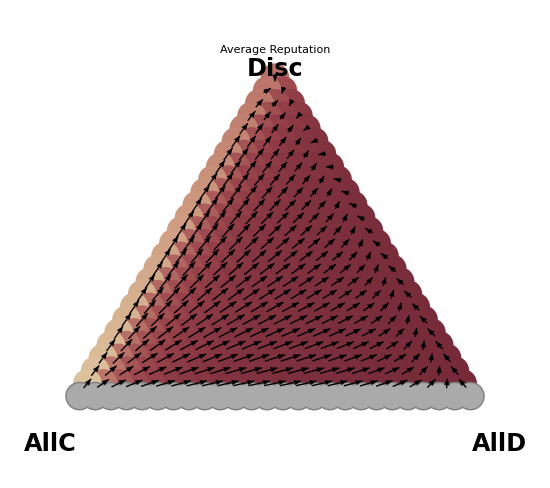

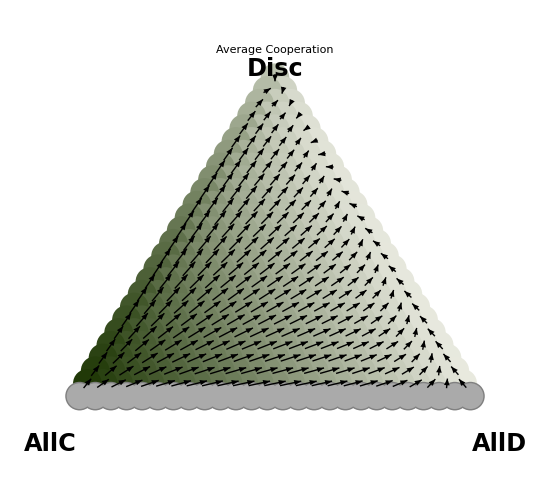

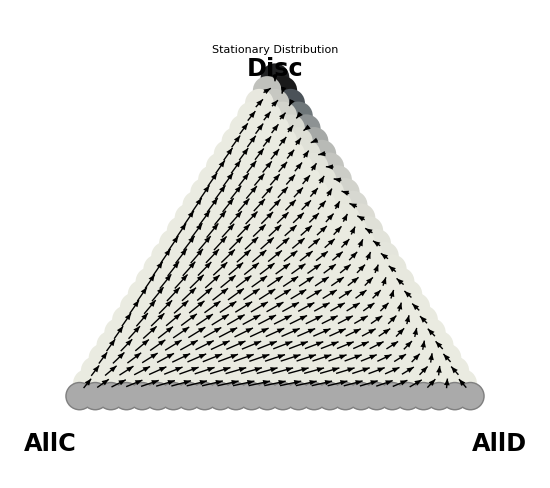

```mathematica
(* Transform the points to be ready to plot*)
d = 60 Degree;
(* Change valid states to valid coordinate states by changing coordinate system *)
transformMatrix ={{N[Cos[-d*2]],N[Sin[-d*2]]},{N[Cos[-d]],N[Sin[-d]]}};

(*Perform matrix transformation on points*)
transformedPoints=validAAstates.transformMatrix;
allTransformedPoints = possibleAAstates.transformMatrix;
transformedGradients = gradients.transformMatrix;
vectorField=Transpose[{allTransformedPoints,transformedGradients}];

invalidtransformedPoints=notvalidAAstates.transformMatrix;
allinvalidTransformedPoints = notpossibleAAstates.transformMatrix;

(*General Plotting*)
plotRange={{-popsize,popsize},{-popsize,0}};
(*plotVectorField=ListVectorPlot[vectorField,PlotRange->plotRange, VectorScaling->Automatic, VectorPoints->All,VectorColorFunction->"Rainbow"];*)
plotVectorField=ListVectorPlot[vectorField,PlotRange->plotRange, VectorScaling->Automatic, VectorPoints->All, VectorColorFunction->(Black&)];
(*plotGrayTriangle=Graphics[{GrayLevel[0.9],Polygon[{{0,0},{Cos[-d*2]*popsize,Sin[-d*2]*popsize},{Cos[-d]*popsize,Sin[-d]*popsize}}],Red,Point[transformedPoints],PlotRange->plotRange,Axes->False, Boxed->False}];*)
(*Replace original sized triangle with the smaller one*)
plotGrayTriangle=Graphics[{GrayLevel[0.9],Polygon[{{0,0},{Cos[-d*2]*popsize,Sin[-d*2]*popsize},{Cos[-d]*popsize,Sin[-d]*popsize}}],Red,Point[transformedPoints],PlotRange->plotRange,Axes->False, Boxed->False}];
(*labels=Graphics[{Text["Disc",{0,1.5},{0,-1.5}],Text["AllC",{Cos[-d*2]*popsize,Sin[-d*2]*popsize}*1.1,{0,-1.5}],Text["AllD",{Cos[-d]*popsize,Sin[-d]*popsize}*1.1,{0,-1.5}]}];*)
labelFontSize = 24;
labels=Graphics[{Text[Style["Disc",Bold,labelFontSize],{0,2.5},{0,-1.5}],Text[Style["AllC",Bold,labelFontSize],{Cos[-d*2]*popsize,Sin[-d*2]*popsize}*1.15,{0,-2.5}],Text[Style["AllD",Bold,labelFontSize],{Cos[-d]*popsize,Sin[-d]*popsize}*1.15,{0,-2.5}]}];


pointScale = 0.0025*3/Sqrt[popSizeForPlot];

(*Scale for the gradient field*)
minMagnitude=Min[Norm/@gradients];
maxMagnitude=Max[Norm/@gradients];
roundedMaxGradient=Round[maxMagnitude,0.01];
gradientLegendReputations=BarLegend[{"Rainbow",{0,roundedMaxGradient}},LegendLabel->Placed["Gradient of Selection",Left, Rotate[#,90Degree]&],LegendLayout->"Column",LegendMarkerSize->450,LabelStyle->{FontSize->16, Black},Ticks->{Range[0,roundedMaxGradient,0.01],Automatic}];

(*Invalid points in AA gradient*)
notvalidPointsPlot=Graphics[{PointSize[popSizeForPlot*pointScale],Darker[Gray],Point/@invalidtransformedPoints}];
(*allnotvalidPointsPlot=Graphics[{PointSize[popSizeForPlot*pointScale],Darker[Gray],Point/@allinvalidTransformedPoints}];*)
allnotvalidPointsPlot=Graphics[{PointSize[popSizeForPlot*pointScale],Gray,Point/@allinvalidTransformedPoints,
PointSize[popSizeForPlot*pointScale*0.9],Lighter[Gray],Point/@allinvalidTransformedPoints}];

If[nAAs == 0 || fixedAAstrategy == False,notvalidPointsPlot = Graphics[]; allnotvalidPointsPlot = Graphics[]];

(*Change color of triangles to be between red and blue for reputations*)
colorsRep=ColorData["RedBlueTones"]/@reputations;
coloredPointsRep=Transpose[{colorsRep,Point/@allTransformedPoints}];
reputationPointsPlot = Graphics[{PointSize[popSizeForPlot*pointScale],coloredPointsRep}];
colorLegendReputations=BarLegend[{"RedBlueTones",{0,1}},LegendLabel->Placed["Average Reputation",Left, Rotate[#,90Degree]&],LegendLayout->"Column",LegendMarkerSize->450,LabelStyle->{FontSize->16, Black}];
repPlot = Style[Row[{Show[plotGrayTriangle,reputationPointsPlot,plotVectorField, allnotvalidPointsPlot,labels,PlotLabel->"Average Reputation",LabelStyle->{FontSize->20, Black,Bold},ImageSize->550],colorLegendReputations}],LineBreakWithin->False]

(*Change color of triangles to be between Black and Green for reputations*)
(*nBins =100000;
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MPLColorMap["Viridis"];
discretizedCoop = Floor[Rescale[cooperation,{Min[cooperation],Max[cooperation]},{0,nBins}]]/(nBins-1);*)
customRepColor[color_:RGBColor[0.1,0.2,0.0]]:=Blend[{ColorData[{"GrayTones","Reverse"}][0],color},#]&
colorsCoop=customRepColor[]/@cooperation;
coloredPointsCoop=Transpose[{colorsCoop,Point/@allTransformedPoints}];
cooperationPointsPlot = Graphics[{PointSize[popSizeForPlot*pointScale],coloredPointsCoop}];
colorLegendReputations=BarLegend[{customRepColor[],{0,1}},LegendLabel->Placed["Average Cooperation",Left, Rotate[#,90Degree]&],LegendLayout->"Column",LegendMarkerSize->450,LabelStyle->{FontSize->16, Black}];
coopPlot = Style[Row[{Show[plotGrayTriangle,cooperationPointsPlot,plotVectorField, allnotvalidPointsPlot,labels,PlotLabel->"Average Cooperation",LabelStyle->{FontSize->20, Black,Bold},ImageSize->550],(*gradientLegendReputations*),colorLegendReputations}], LineBreakWithin->False]

(*Change color of triangles to be between white and fuchsia for stationary dist*)

normalizedStationary=Rescale[stationary,{Min[stationary],Max[stationary]},{0,1}];
colorsStatDist=ColorData[{"GrayTones","Reverse"}]/@normalizedStationary;
coloredPointsStatDist=Transpose[{colorsStatDist,Point/@allTransformedPoints}];
StatDistPointsPlot = Graphics[{PointSize[popSizeForPlot*pointScale],coloredPointsStatDist}];
colorLegendStatDist=BarLegend[{"GrayTones","Reverse"},LegendLabel->Placed["Stationary Distribution (Rescaled)",Left, Rotate[#,90Degree]&],LegendLayout->"Column",LegendMarkerSize->450,LabelStyle->{FontSize->16, Black}];
distPlot = Style[Row[{Show[plotGrayTriangle,StatDistPointsPlot,plotVectorField, allnotvalidPointsPlot,labels,PlotLabel->"Stationary Distribution",LabelStyle->{FontSize->20, Black,Bold},ImageSize->550],(*gradientLegendReputations*),colorLegendStatDist}],LineBreakWithin->False]
```

```mathematica
(*Optional: export the plots to pdf*)
SetDirectory["~/Desktop/PhD/1 - Dynamics of IR in hybrid populations/FinalSimplexes"];
SetOptions["stdout",PageWidth->Infinity];
Export[simplexFileName<>"rep.pdf",repPlot ];
Export[simplexFileName<>"coop.pdf",coopPlot];
Export[simplexFileName<>"dist.pdf",distPlot];
```

## Cooperation Index

```mathematica
allStates= Select[Flatten[Table[{nAllC,nAllD, popsize-nAllC-nAllD},{nAllC,0,popsize,1},{nAllD,0,popsize,1}],1],Total[#[[1]]+#[[2]]]<=popsize&];
allAAstates = If[fixedAAstrategy,Select[allStates,Which[indexOfAA==0,#[[1]]>=nAAs,indexOfAA==1,#[[2]]>=nAAs,indexOfAA==2,#[[3]]>=nAAs,True,False]&],allStates];

sumCoop[allc_,alld_] := StationaryDistStrategy[[Position[allAAstates,{allc,alld,popsize-allc-alld}][[1,1]]]] *(avgCoopAllC[allc,alld]*allc/popsize+avgCoopAllD[allc,alld]*alld/popsize+avgCoopDisc[allc,alld]*(popsize-allc-alld)/popsize);

coopIndex=Sum[Sum[
If[ fixedAAstrategy == False||(indexOfAA==0&&allc>=nAAs) ,sumCoop[allc,alld],
If[indexOfAA==1&&alld>=nAAs,sumCoop[allc,alld],
If[indexOfAA==2&&popsize-allc-alld>=nAAs,sumCoop[allc,alld],0 ]]],{alld,0,popsize-allc}],{allc,0,popsize}];
coopIndex
Export[simplexFileName<>"coop.txt",coopIndex]
```

Divide::indet: Indeterminate expression 0./0 encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

0.115883

SH_AA4_coop.txt

## ------------------------------------------- Test Zone ---------------------------------------------------------------

```mathematica
(* -----------------------------------------------------
Test zone 
----------------------------------------*)
```